```mathematica
Clear["Global`*"]
```

```mathematica
ppresults=Import["/home/r-matrixsuperconductor/Desktop/transfer to 7th floor computer/NS^4 shot noise/200 points/received from 7th floor computer/ppresults3.mx"];
hhresults=Import["/home/r-matrixsuperconductor/Desktop/transfer to 7th floor computer/NS^4 shot noise/200 points/received from 7th floor computer/hhresults3.mx"];
phresults=Import["/home/r-matrixsuperconductor/Desktop/transfer to 7th floor computer/NS^4 shot noise/200 points/received from 7th floor computer/phresults3.mx"];
```

```mathematica
energies=N[Table[1*10^-7*i+0.00008,{i,0,200}]];
totalresults=Table[{energies[[i]],ppresults[[i,2]]+hhresults[[i,2]]+phresults[[i,2]]},{i,1,Length[energies]}];
```

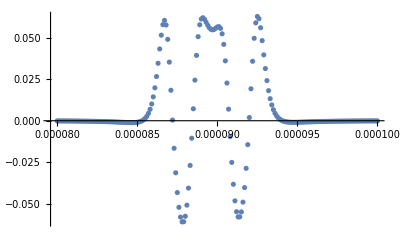

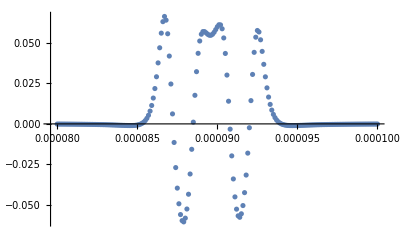

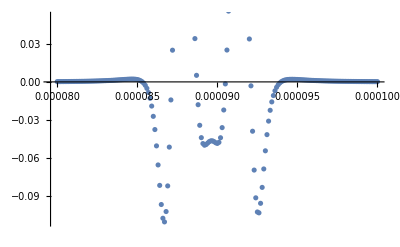

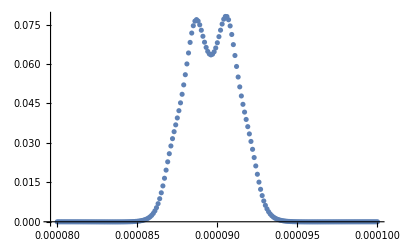

```mathematica
ListPlot[ppresults]
ListPlot[hhresults]
ListPlot[phresults]
ListPlot[totalresults]
```

```mathematica
smatrix=Import["/home/r-matrixsuperconductor/Desktop/NSNSNSNSN/NSNSNSNSN_Smatrix_from_Tmatrix.mx"]/.{x[1]->x1,x[2]->x2,x[3]->x3,x[4]->x4,x[5]->x5,x[6]->x6,x[7]->x7,x[8]->x8};
```

```mathematica
rppLL=smatrix[[1,1]];
rphLL=smatrix[[1,2]];
tppLR=smatrix[[1,3]];
tphLR=smatrix[[1,4]];
rhpLL=smatrix[[2,1]];
rhhLL=smatrix[[2,2]];
thpLR=smatrix[[2,3]];
thhLR=smatrix[[2,4]];
tppRL=smatrix[[3,1]];
tphRL=smatrix[[3,2]];
rppRR=smatrix[[3,3]];
rphRR=smatrix[[3,4]];
thpRL=smatrix[[4,1]];
thhRL=smatrix[[4,2]];
rhpRR=smatrix[[4,3]];
rhhRR=smatrix[[4,4]];
```

```mathematica
x2=x1+ls1;
x3=x2+ln1;
x4=x3+ls2;
x5=x4+ln2;
x6=x5+ls3;
x7=x6+ln3;
x8=x7+ls4;
qp=Sqrt[2*(EF+e)];
qh=Sqrt[2*(EF-e)];
kp=Sqrt[2*(EF+Sqrt[e^2-DD^2])];
kh=Sqrt[2*(EF-Sqrt[e^2-DD^2])];    
u=Sqrt[(1+Sqrt[e^2-DD^2]/e)/2];
v=Sqrt[(1-Sqrt[e^2-DD^2]/e)/2];
x1=-2100;
ls1=200;
ls2=200;
ls3=200;
ls4=200;
ln1=800;
ln2=1800;
ln3=800;
EF=0.001307;
DD=0.00053814;
```

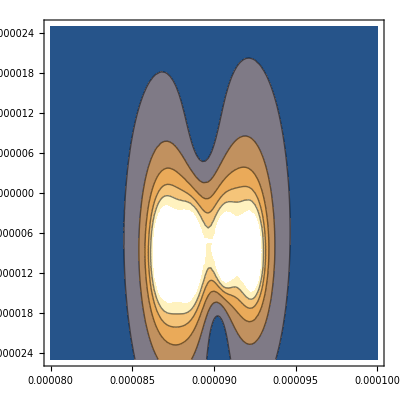

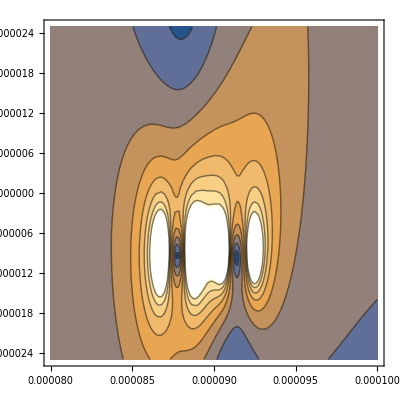

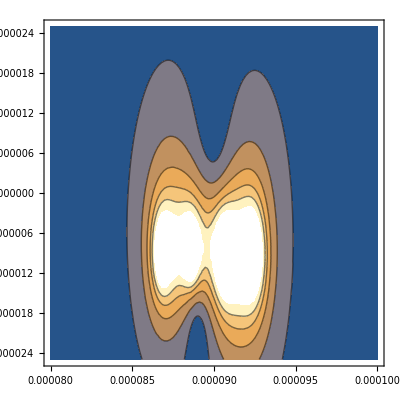

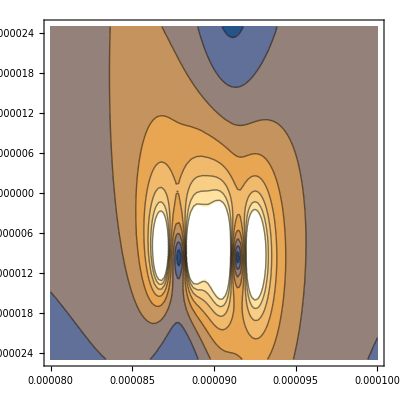

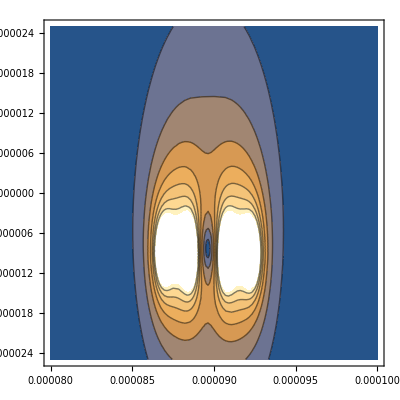

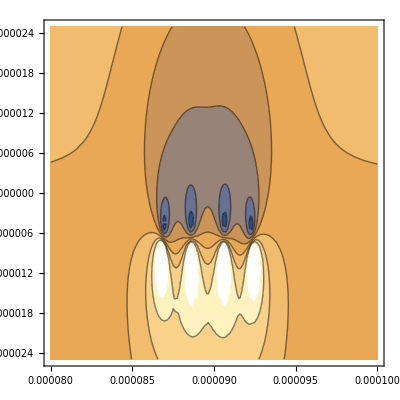

```mathematica
e=er+I*ei;
ContourPlot[Abs[N[tppLR]],{er,0.00008,0.0001},{ei,-2.5*10^-6,2.5*10^-6}]
ContourPlot[Abs[N[rppLL]],{er,0.00008,0.0001},{ei,-2.5*10^-6,2.5*10^-6}]
ContourPlot[Abs[N[thhLR]],{er,0.00008,0.0001},{ei,-2.5*10^-6,2.5*10^-6}]
ContourPlot[Abs[N[rhhLL]],{er,0.00008,0.0001},{ei,-2.5*10^-6,2.5*10^-6}]
ContourPlot[Abs[N[tphLR]],{er,0.00008,0.0001},{ei,-2.5*10^-6,2.5*10^-6}]
ContourPlot[Abs[N[rphLL]],{er,0.00008,0.0001},{ei,-2.5*10^-6,2.5*10^-6}]
e=.
```